#### Явный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Explicit_eiler500.txt"]],Table[Real,n+1]];
T = {};
```

```mathematica
For[i=1,i≤500,i++,T = Append[T,{plots⟦i⟧⟦2⟧,plots⟦i⟧⟦3⟧}]]
```

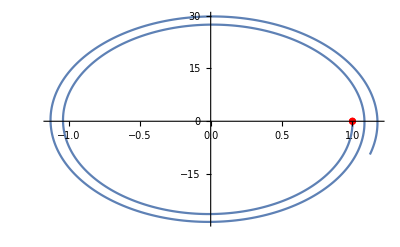

```mathematica
Show[ListLinePlot[T],ListPlot[{T⟦1⟧},PlotStyle->Red]]
```

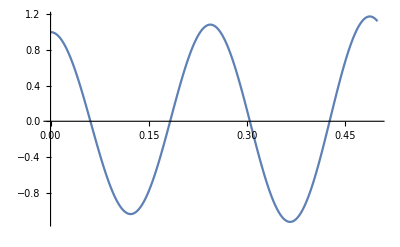

```mathematica
Realy={};
For[i=1,i≤500,i++,Realy = Append[Realy,{plots⟦i⟧⟦1⟧,plots⟦i⟧⟦2⟧}]]
ListLinePlot[Realy]
```

#### Неявный

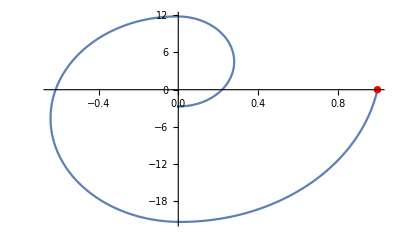

```mathematica
NotebookDirectory[];
n = 2;
plotsIm=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Implicit_eiler500.txt"]],Table[Real,n+1]];
TIm = {};
For[i=1,i≤500,i++,TIm = Append[TIm,{plotsIm⟦i⟧⟦2⟧,plotsIm⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TIm],ListPlot[{TIm⟦1⟧},PlotStyle->Red]]
```

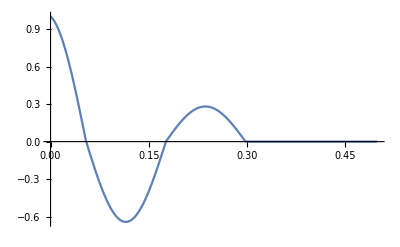

```mathematica
RealyIm={};
For[i=1,i≤500,i++,RealyIm = Append[RealyIm,{plotsIm⟦i⟧⟦1⟧,plotsIm⟦i⟧⟦2⟧}]]
ListLinePlot[RealyIm]
```

#### Симметричная схема

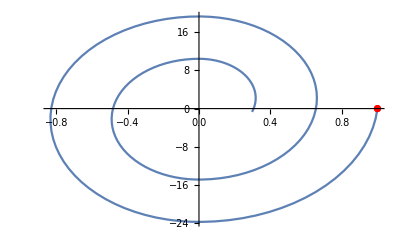

```mathematica
NotebookDirectory[];
n = 2;
plotsSym=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Sym_scheme.txt"]],Table[Real,n+1]];
TSym = {};
For[i=1,i≤Length[plotsSym],i++,TSym = Append[TSym,{plotsSym⟦i⟧⟦2⟧,plotsSym⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TSym],ListPlot[{TSym⟦1⟧},PlotStyle->Red]]
```

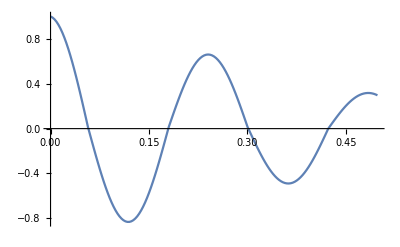

```mathematica
RealySym={};
For[i=1,i≤Length[plotsSym],i++,RealySym = Append[RealySym,{plotsSym⟦i⟧⟦1⟧,plotsSym⟦i⟧⟦2⟧}]]
ListLinePlot[RealySym]
```